## Switching Time Analysis Pile Driver Ashwin & Aaron

```mathematica
casetimes = {(√(2 vop^2+4 a l)-2 vop)/(2 a),(√(vop^2+ 2 a l)- vop)/a,(√(vop^2+ 2 a l)- vop)/a+(π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m)),(√(vop^2+ 2 a l)- vop)/a+2((π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m))),2((√(vop^2+ 2 a l)- vop)/a+(π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m)))};

deltaT[ts_,vop_,a_,m_,k_,l_]:=Piecewise[{{deltaTc1[ts,vop,a,l], vop^2<2 a l && ts<casetimes⟦1⟧}, {deltaTc2[ts,vop,a,m,k,l], casetimes⟦1⟧⩽ts<casetimes⟦2⟧}, {deltaTc3[ts,vop,a,m,k,l], casetimes⟦2⟧⩽ts<casetimes⟦3⟧}, {deltaTc4[ts,vop,a,m,k,l], ts=casetimes⟦3⟧}, {deltaTc5[ts,vop,a,m,k,l], casetimes⟦3⟧<ts<casetimes⟦4⟧}, {deltaTc6[ts,vop,a,m,k,l], casetimes⟦4⟧⩽ts<casetimes⟦5⟧}, {casetimes⟦5⟧, ts⩾casetimes⟦5⟧}}]
```

```mathematica
deltaTc1[ts_,vop_,a_,l_]:=2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))
deltaTc2[ts_,vop_,a_,m_,k_,l_]:=Module[{F,ω,vts,s1,v1a,t1a,t1b,t2a,t2b},F = m a;ω = √(k/m);vts = vop+a ts;s1 = vop + 1/2 a ts^2;v1a = √(vts^2- 2 a (l-s1));t1a = (v1a-vts)/a;t1b = ArcTan[(v1a k)/(ω F)]/ω;t2a = ArcTan[(v1a k)/(ω F)]/ω;
t2b = (√(v1a^2+ 2 a l)-v1a)/a;

ts + t1a + t1b +t2a +t2b
]
deltaTc3[ts_,vop_,a_,m_,k_,l_]:=Module[{F,ω,yt1b,t1b,vt1b,C,y0c3,t1c,t2a,v2a,t2b},F = m a;ω = √(k/m);t1b = ts - casetimes⟦2⟧;yt1b = (√(vop^2+ 2 a l))/ω Sin[ω t1b]-F/ω Cos[ω t1b]+F/k;vt1b = √(vop^2+ 2 a l)Cos[ω t1b]+F/k ω Sin[ω t1b];t1c = ArcTan[vt1b/(ω (yt1b+F/k))]/ω;C = -1/2 m vop^2-2 F yt1b; y0c3 = (-F + √(F^2-2 k C))/k;t2a = ArcCos[F/(F + k y0c3)]/ω;v2a = √(k/m y0c3^2- 2 F/m y0c3);t2b = (√(v2a^2+ 2 a l)- v2a)/a;ts+t1c+t2a+t2b
]
deltaTc4[ts_,vop_,a_,m_,k_,l_]:=Module[{F,ω,trev,y0,tfor1,v4,vimp,tfor2},F = m a;ω = √(k/m);trev=casetimes⟦3⟧;y0 = (F+√(F^2+k m vop^2+2F l k))/k;tfor1 = ArcCos[F/(F+k y0)]/ω;v4 = √(k/m y0^2+(2F y0)/m);vimp = √(v4^2+ 2 a l);tfor2 = (vimp-v4)/a;ts+tfor1+tfor2
]
deltaTc5[ts_,vop_,a_,m_,k_,l_]:=Module[{F,ω,t2a,y0,y2a,v2a,t2b,v2b,vimp,t2c},F = m a;ω = √(k/m); t2a = ts - casetimes⟦3⟧;y0 = (F+√(F^2+k m vop^2+2F l k))/k;y2a = (y0-F/k)Cos[ω t2a]+F/k;v2a = (F/k-y0)ω Sin[ω t2a]; t2b = (2 (ArcTan[(√(k (v2a^2 k+y2a^2 k ω^2+2 y2a F ω^2))+v2a k)/(ω (y2a k+2 F))]))/ω;v2b = √(2/m(1/2 k y0^2- F(2 y2a - y0)));vimp = √(v2b^2+2 a l);t2c = (vimp - v2b)/a; ts+t2b+t2c
]
deltaTc6[ts_,vop_,a_,m_,k_,l_]:=Module[{t1,v1,vts,sts,vimp,t2b},t1 = casetimes⟦4⟧;v1 = √(vop^2+2 a l);vts = v1-a(ts-t1);sts = v1(ts-t1)-1/2 a(ts-t1)^2;vimp = √(vts^2+2a(l-sts));t2b = (vimp - vts)/a;ts+t2b
]
```

## Simplify math

```mathematica
FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))]
```

2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

```mathematica
ω = √(k/m);

FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))+ω]
```

√(k/m)+2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

## Make simple plot of ΔT vs t_s

Set::setraw: Cannot assign to raw object -0.999959.

Set::setraw: Cannot assign to raw object -0.959143.

Set::setraw: Cannot assign to raw object -0.918326.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

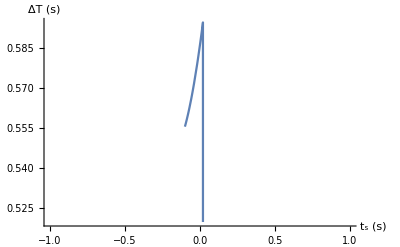

```mathematica
a=3.67;
vop = 0.9*1.6;
l = 0.03;
m=0.0005;
k = 50;
Plot[deltaT[ts,vop,a,m,k,l],{ts,-1,1},
AxesLabel->{"t_s (s)","ΔT (s)"}
]

(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## Make plot of ΔT vs t_s

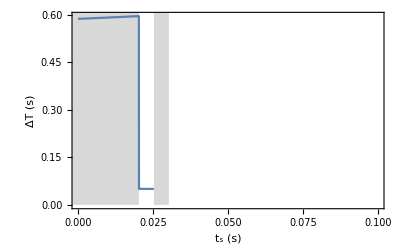

```mathematica
a=3.67;
vop = 0.9*1.6;
l = 0.03;
m=0.0005;
k = 50;

Plot[deltaT[ts,vop,a,m,k,l],{ts,0,0.1},
Frame->{True,True,False,False},FrameLabel->{"t_s (s)","ΔT (s)"},
(*Epilog->{Gray,Thin,Table[Line[{{tc,0},{tc,100}}],{ tc, casetimes }]}*)
Prolog-> {Gray,Opacity[0.3],Thin,Table[Rectangle[{casetimes⟦2tc-1⟧,0},{casetimes⟦2tc⟧,100}],{ tc, 1,Floor[Length[casetimes]/2] }]}

]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

```mathematica
casetimes//N
```

{-0.100563,0.0203078,0.0252993,0.0302909,0.0505987}

## (simple) Make plot of ΔT vs v_(0^+)

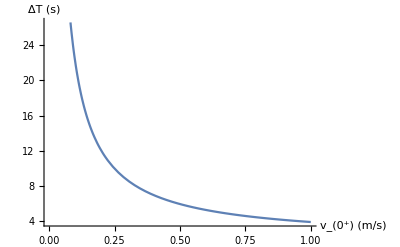

```mathematica
a=1;
ts = 1/2;
l = 0.1;
Plot[deltaTc1[ts,a,vop,l],{vop,0,1},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"}
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## better plot of ΔT vs v_(0^+)

Set::setraw: Cannot assign to raw object 0.027.

Set::setraw: Cannot assign to raw object 0.04.

Set::setraw: Cannot assign to raw object 0.06.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

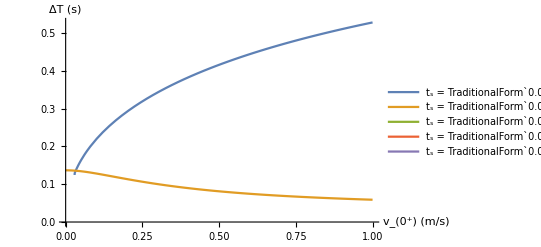

```mathematica
a=3.67;

l = 0.03;
m=0.0005;
k = 50;
tsVals = {0.01,0.022,0.027,0.040,0.06};
Clear[vop]
Plot[Evaluate[Table[deltaT[ts,vop,a,m,k,l],{ts,tsVals}]],{vop,0,1},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"},
PlotLegends->Table[StringForm["t_s = ``",ts],{ts,tsVals}]
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```